```mathematica
f[x_]:=1/20 x^4-x^2-x+10
y[x_,n_]:=10/Integrate[f[y]^n,{y,-5,5}] Integrate[f[y]^n,{y,-5,x}]-5
```

```mathematica
?InterpolatingPolynomial
```

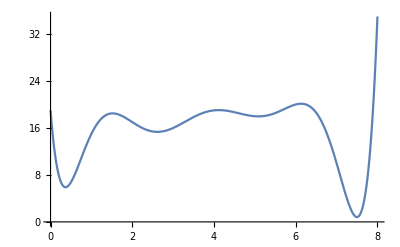

```mathematica
g[x_]:=InterpolatingPolynomial[{4, 0, 2, 1, 4, 3, 5,-5,20},x+1]+15
yg[x_,n_]:=8/Integrate[g[y]^n,{y,0,8}] Integrate[g[y]^n,{y,0,x}]
Plot[g[x],{x,0,8}]
```

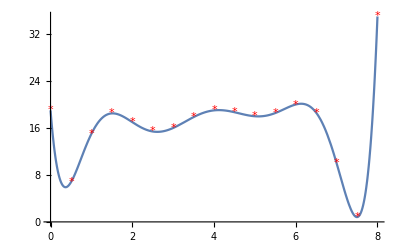

```mathematica
Show[
Plot[g[x],{x,0,8}],
ListPlot[Table[{x,g[x]},{x,0,8,0.5}],PlotMarkers->"*",PlotStyle->Red]
]
```

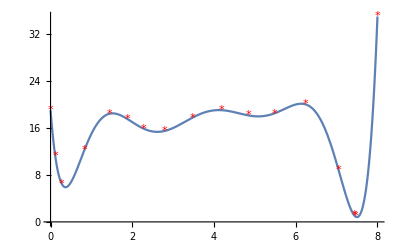

```mathematica
With[{n=3},
Show[
Plot[g[x],{x,0,8}],
ListPlot[Table[{yg[x,n],g[yg[x,n]]},{x,0,8,0.5}],PlotMarkers->"*",PlotStyle->Red]
]]
```

```mathematica
yg[7,3]
```

7.43285

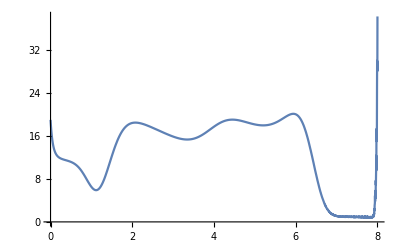

```mathematica
Plot[g[yg[x,3]],{x,0,8}]
```

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

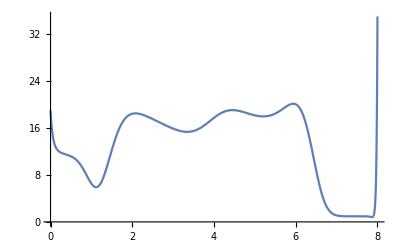

```mathematica
Plot[g[yg[x,3]],{x,0,8}]
```

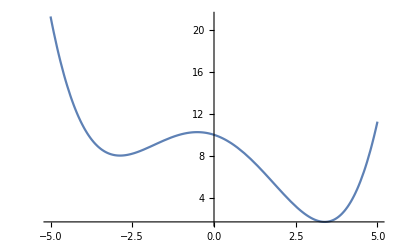

```mathematica
Plot[f[x],{x,-5,5}]
```

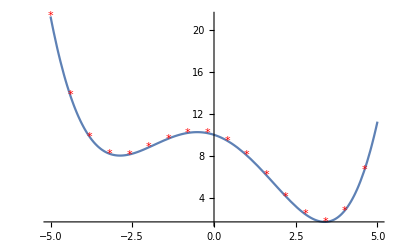

```mathematica
Show[
Plot[f[x],{x,-5,5}],
ListPlot[Table[{x,f[x]},{x,-5,5,0.6}],PlotMarkers->"*",PlotStyle->Red]
]
```

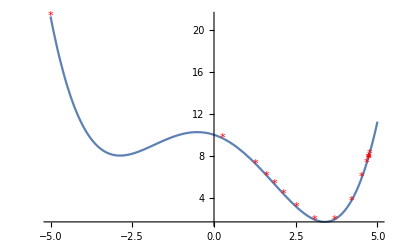

```mathematica
With[{n=4},
Show[
Plot[f[x],{x,-5,5}],
ListPlot[Table[{y[x,n],f[y[x,n]]},{x,-5,5,0.6}],PlotMarkers->"*",PlotStyle->Red]
]]
```

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

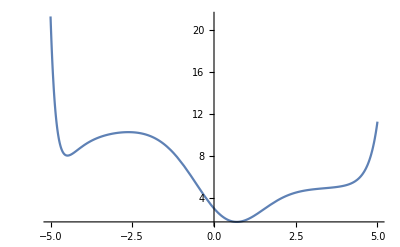

```mathematica
Plot[f[Evaluate@y[x,2]],{x,-5,5}]
```